{{-15,-6},{-14,13},{-10,-3},{-8,13},{-3,-9},{0,11},{4,13},{10,-13},{10,-19}}

{{3,13}}

{{-9,3}}

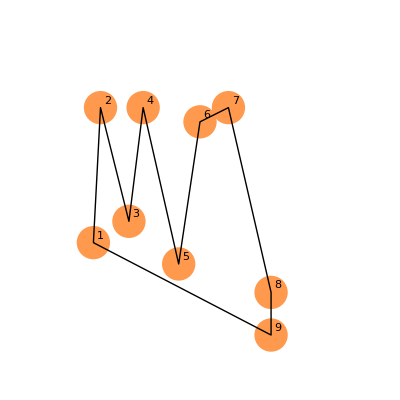

```mathematica
P[n_]:=Table[{Random[Integer, {-20, 20}],Random[Integer, {-20, 20}]},{n}]
MPolinom = {{-15,-6},{-14,13},{-10,-3},{-8,13},{-3,-9},{0,11},{4,13},{10,-13},{10,-19}}
MPoint ={{3,13}}
 P[1]
Graphics[{PointSize[0.03],RGBColor[.4, 1, .5], Point[MPoint], PointSize[0.06], RGBColor[1, .6, .3], Point/@MPolinom, Black, MapIndexed[Text[#2⟦1⟧, #1+{1,1}]&,MPolinom], Line[Append[MPolinom, MPolinom⟦1⟧]]}, AspectRatio->Automatic, PlotRange->{{-23, 23},{-23,23}}]
```

```mathematica
xMin = Min [Table[MPolinom[[i]][[1]], {i, 1,  Length[MPolinom]}]];
yMin = Min [Table[MPolinom[[i]][[2]], {i, 1,  Length[MPolinom]}]];
xMax = Max[Table[MPolinom[[i]][[1]], {i, 1,  Length[MPolinom]}]];
yMax = Max [Table[MPolinom[[i]][[2]], {i, 1,  Length[MPolinom]}]];
```

```mathematica
xMin
xMax
yMin
yMax
```

-15

10

-19

13

```mathematica
MPoint[[1,2]]
If[MPoint⟦1,1⟧<xMin || MPoint⟦1,1⟧>xMax||MPoint⟦1,2⟧<yMin || MPoint⟦1,2⟧>yMax, Print["Точка лежит вне полинома"]]



IsInQ[{p1_, p2_}, p0_]:=Det[{p2-p1,p0-p1}]==0
TmpPoint = {-20};
AppendTo[TmpPoint, MPoint⟦1,2⟧];
TmpPoint
```

13

{-20,13}

```mathematica
TmpLine = {};
AppendTo[TmpLine,TmpPoint];
AppendTo[TmpLine,MPoint⟦1⟧];
TmpLine
```

{{-20,13},{3,13}}

```mathematica
For[i = 1, i<10, i++,{If[IsInQ[TmpLine,MPolinom⟦i⟧],{TmpLine  = Delete[TmpLine,{1,2}], AppendTo[TmpLine⟦1⟧, Random[Integer, {-20, 20}]], i=1}]}]
```

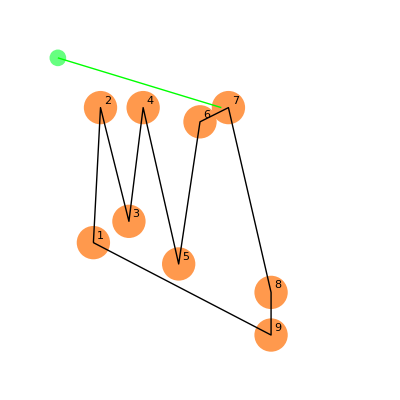

```mathematica
Graphics[{PointSize[0.03],RGBColor[.4, 1, .5], Point/@TmpLine, Green, Line[TmpLine], PointSize[0.06], RGBColor[1, .6, .3], Point/@MPolinom, Black, MapIndexed[Text[#2⟦1⟧, #1+{1,1}]&,MPolinom], Line[Append[MPolinom, MPolinom⟦1⟧]]}, AspectRatio->Automatic, PlotRange->{{-23, 23},{-23,23}}]
```

```mathematica
ICount = 0;
n=1;
While[n<9, {
d1 = Det[{MPolinom⟦n+1⟧-MPolinom⟦n⟧,TmpLine⟦1⟧-MPolinom⟦n⟧}];
d2 = Det[{MPolinom⟦n+1⟧-MPolinom⟦n⟧,TmpLine⟦2⟧-MPolinom⟦n⟧}];
d3 = Det[{TmpLine⟦2⟧-TmpLine⟦1⟧,MPolinom⟦n⟧-TmpLine⟦1⟧}];
d4 = Det[{TmpLine⟦2⟧-TmpLine⟦1⟧,MPolinom⟦n+1⟧-TmpLine⟦1⟧}];
If[d1*d2≤0 && d3*d4 ≤0,ICount ++]}n++]
```

```mathematica
d1 = Det[{MPolinom⟦9⟧-MPolinom⟦1⟧,TmpLine⟦1⟧-MPolinom⟦1⟧}];
d2 = Det[{MPolinom⟦9⟧-MPolinom⟦1⟧,TmpLine⟦2⟧-MPolinom⟦1⟧}];
d3 = Det[{TmpLine⟦2⟧-TmpLine⟦1⟧,MPolinom⟦9⟧-TmpLine⟦1⟧}];
d4 = Det[{TmpLine⟦2⟧-TmpLine⟦1⟧,MPolinom⟦9⟧-TmpLine⟦1⟧}];
If[d1*d2≤0 && d3*d4 ≤0,ICount ++]
ICount
```

0

```mathematica
If[Mod[ICount,2]==1, "Точка лежит внутри полигона", "Точка лежит снаружи полигона"]
```

Точка лежит снаружи полигона